```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
data=Import["infoseq_admax_14.csv"]
```

{{6,0.00131025},{57,0.00361678},{32,0.00725399},{66,0.013035},{75,0.023307},{88,0.0395135},{44,0.0631357},{90,0.0970919},{39,0.143022},{46,0.193748},{74,0.250989},{63,0.307693},{53,0.36161},{40,0.408827}}

```mathematica
dat=Import["infoseq_amax_14.csv"]
```

{{6,0.00131025},{57,0.00361678},{32,0.00725399},{66,0.013035},{75,0.023307},{88,0.0395135},{44,0.0631357},{90,0.0970919},{39,0.143022},{46,0.193748},{74,0.250989},{63,0.307693},{53,0.36161},{40,0.408827}}

```mathematica
dato=Import["infoseq_afromc_23.csv"]
```

{{6,0.0013201},{57,0.00366211},{32,0.0073734},{66,0.0132599},{75,0.023237},{88,0.03897},{93,0.0602239},{22,0.089574},{14,0.117802},{21,0.132639},{43,0.123568},{89,0.0967005},{70,0.0653778},{90,0.0392137},{94,0.0217774},{30,0.0115567},{77,0.00595885},{85,0.0030284},{24,0.00152627},{27,0.000766231},{84,0.000383885},{23,0.000192118},{86,0.0000961032}}

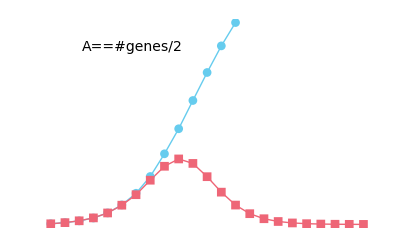

```mathematica
ListPlot[{dat[[;;,2]],dato[[;;,2]]},Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dato],Style[#,12]&/@dato[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A=="#genes/2",14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_AhalfC",%]
```

progression_AhalfC.pdf

```mathematica
Log[2,n]//N
```

12.5577

```mathematica
2^12
```

4096

```mathematica
2^10
```

1024

```mathematica
Binomial[94,10]//N
```

9.04126×10^12

```mathematica
n/2^10//N
```

5.8877

```mathematica
dat1e3=Import["infoseq_22.csv"]
```

{{9,0.00714047},{67,0.0127164},{13,0.0179127},{16,0.0227846},{17,0.0294803},{59,0.0361631},{70,0.0497722},{39,0.0759585},{43,0.120456},{89,0.19676},{93,0.30768},{55,0.458223},{76,0.646054},{22,0.850405},{66,1.0488},{8,1.21224},{92,1.32999},{21,1.40668},{77,1.44917},{62,1.47285},{48,1.48685},{25,1.49386}}

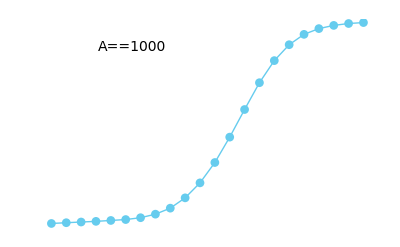

```mathematica
ListPlot[dat1e3[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat1e3],Style[#,12]&/@dat1e3[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A==1000,14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_A1e3",%]
```

progression_A1e3.pdf

```mathematica
dat1e6=Import["infoseq_1000000_30.csv"]
```

{{9,8.99509×10^-6},{63,0.0000223753},{13,0.0000423247},{11,0.0000819628},{82,0.000152251},{83,0.000281068},{5,0.00047234},{1,0.000690619},{67,0.000820893},{53,0.000933726},{74,0.00103995},{16,0.00114339},{40,0.0012529},{54,0.00137422},{57,0.00154244},{51,0.00176335},{29,0.0020942},{66,0.00263217},{22,0.00342926},{70,0.00451066},{89,0.00582635},{77,0.00725472},{4,0.0086469},{20,0.00986983},{92,0.0108101},{93,0.0114654},{76,0.0118823},{27,0.0121235},{6,0.0122629},{94,0.0123454}}

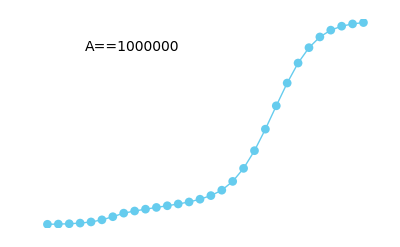

```mathematica
ListPlot[dat1e6[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat1e6],Style[#,12]&/@dat1e6[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A==10^6,14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_A1e6",%]
```

progression_A1e6.pdf

```mathematica
{dato[[;;,1]],dat1000[[;;,1]],dat1e6[[;;,1]]}//MF
```

({6,57,32,66,75,88,93,22,14,21,43,89,70}
{9,67,13,16,17,59,70,39,43,89,93,55,76,22,66,8,92}
{9,63,13,11,82,83,5,1,67,53,74,16,40,54,57,51,29,66,22,70,89,77,4,20})

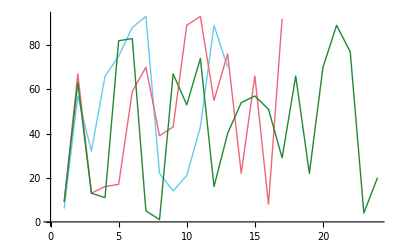

```mathematica
ListPlot[{dato[[;;,1]],dat1000[[;;,1]],dat1e6[[;;,1]]},Joined->True]
```